```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
TLD[t_]:=t*IdentityMatrix[25]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
leads[25]
```

{{{0.-0.848854 ⅈ,0.500319+0. ⅈ,0.+0.170564 ⅈ,-0.00148296+0. ⅈ,0.+0.0219777 ⅈ,0.00302035+0. ⅈ,0.+0.0116615 ⅈ,-0.00381066+0. ⅈ,0.+0.0000550464 ⅈ,0.0030296+0. ⅈ,0.+0.00421847 ⅈ,-0.00148449+0. ⅈ,0.+0.000330511 ⅈ,0.000363268+0. ⅈ,0.+0.000839972 ⅈ,-0.0000187093+0. ⅈ,0.+0.000473503 ⅈ,3.77068×10^-6+0. ⅈ,0.+0.000321694 ⅈ,-0.0000155762+0. ⅈ,0.+0.000184309 ⅈ,4.2504×10^-6+0. ⅈ,0.+0.000109971 ⅈ,-1.79988×10^-6+0. ⅈ,0.+0.0000334653 ⅈ},23,{0.+0.0000334653 ⅈ,23,0.-0.848854 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_]:=dist[total]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,25]],total]],First],10000]
```

```mathematica
dist[10][[1]]
```

{{5,22},{22,6},{28,7},{32,8},{40,20},{78,7},{81,19},{87,17},{100,1},{100,5}}

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,number_]:= Module[{sizeoflead=25,abc=dist[total][[number]]},
recurs=Module[{J1=LEFT[ω,25]},
Do[
J1=Inverse[IdentityMatrix[25]-Inverse[Module[{J=β[ω,δ,t,ϵ,25]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,25].J1.T[1,25]].Inverse[Module[{J=β[ω,δ,t,ϵ,25]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,25}];J1=J1];ir=Inverse[IdentityMatrix[25]-LEFT[ω,25].TLD[1].recurs.TLD[1]].LEFT[ω,25];il=Inverse[IdentityMatrix[25]-recurs.TLD[1].LEFT[ω,25].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
CA[0,0.0001,1,0,1,10,1]
```

0.005335

```mathematica
pris:=pris=Table[{ω,CA[ω,0.0001,1,0,0,100,1]},{ω,Range[0,3,0.01]}]
```

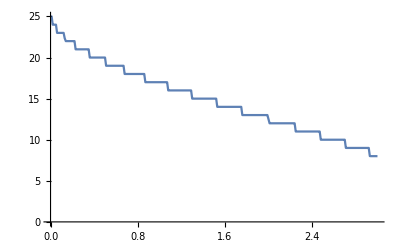

```mathematica
ListLinePlot[pris]
```

```mathematica
Clear[input]
```

```mathematica
input[ϵ_,conc_,num_]:=input[ϵ,conc,num]=ParallelTable[{ω,CA[ω,0.0001,1,0,ϵ,conc,num]},{ω,Range[0,3,0.01]}]
```

```mathematica
Table[Table[Table[Export["~/PhD/fwi/new_inversion/sq_lattice/input_ϵ_"<>ToString[ϵ]<>"_conc_"<>ToString[z]<>"_.dat",input[ϵ,z,num]],{ϵ,Range[0.1,0.7,0.1]}],{z,10,100,10}],{num,10}]
```

```mathematica
Dimensions[%33]
```

{10,10,7}

```mathematica
Table[Export["~/PhD/fwi/new_inversion/sq_lattice/input_"<>ToString[conc]<>"_.dat",input[conc]],{conc,10,70,5}]
```

{~/PhD/fwi/new_inversion/sq_lattice/input_10_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_15_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_20_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_25_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_30_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_35_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_40_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_45_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_50_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_55_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_60_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_65_.dat,~/PhD/fwi/new_inversion/sq_lattice/input_70_.dat}

```mathematica
Clear[in]
```

```mathematica
in[conc_]:=in[conc]= Import["~/PhD/fwi/new_inversion/sq_lattice/input_"<>ToString[conc]<>"_.dat"]
```

```mathematica
Table[Print[v];input[v],{v,Range[5,60,5]}]
```

{{{{0.,21.0929},{0.01,18.7723},{0.02,22.1736},{0.03,22.825},{0.04,22.8087},{0.05,22.4662},{0.06,21.189},{0.07,22.1872},{0.08,22.1929},{0.09,22.1577},{0.1,22.0813},{0.11,21.9184},{0.12,21.4402},{0.13,12.1182},{0.14,21.3858},272,{2.87,8.99992},{2.88,8.99996},{2.89,8.99984},{2.9,8.99992},{2.91,8.99989},{2.92,8.99986},{2.93,8.00786},{2.94,7.99992},{2.95,7.99998},{2.96,7.99992},{2.97,7.99992},{2.98,7.99994},{2.99,7.99992},{3.,7.99996}},98,{1}},10,{1}}
 |  |  |  |

```mathematica
misfit[ϵ_,conc_,num_,a_,b_]:= Integrate[Interpolation[Table[{input[ϵ,conc][[num]][[x,1]],input[ϵ,conc][[num]][[x,2]]/pris[[x,2]]},{x,301}]][y],{y,a,b}]/Abs[b-a]
```

```mathematica
Monitor[Table[Table[Mean[ParallelTable[Mean[Table[misfit[ϵ,50,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.2]}]],{nnn,10}],{ϵ,Range[0.1,0.7,0.1]}],ϵ]
```

{{0.994908,0.99487,0.9951,0.990642,0.989635,0.989547,0.993255,0.994926,0.992179,0.992759},{0.980805,0.993161,0.981323,0.987121,0.983679,0.992966,0.983225,0.985563,0.981318,0.981952},{0.963893,0.978154,0.963151,0.966604,0.968653,0.967138,0.9686,0.970971,0.969627,0.975651},{0.93432,0.953978,0.931694,0.93485,0.944566,0.943651,0.948759,0.935671,0.939566,0.947061},{0.894834,0.923031,0.89529,0.912731,0.903631,0.90816,0.920045,0.905038,0.910644,0.909605},{0.866619,0.892809,0.858956,0.887006,0.875431,0.864005,0.886937,0.87732,0.881896,0.87733},{0.826753,0.865373,0.829991,0.842734,0.852853,0.839591,0.851281,0.850558,0.85499,0.84134}}

```mathematica
Table[Mean[%27[[x]]],{x,7}]
```

{0.992782,0.985111,0.969244,0.941412,0.908301,0.876831,0.845546}

```mathematica
Table[Mean[%22[[x]]],{x,7}]
```

{0.997468,0.996427,0.985847,0.977858,0.967689,0.949653,0.931484}

```mathematica
Around[%29]
```

0.9760.010

```mathematica
pris=ParallelTable[{ω,CA[ω,0.0001,1,0,0,100,1]},{ω,Range[0,3,0.01]}]
```

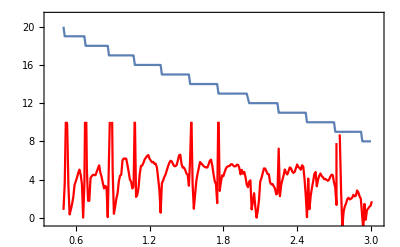

```mathematica
Show[ListPlot[ParallelTable[{ω,CA[ω,0.0001,1,0,0,100,1]},{ω,Range[0.5,3,0.01]}],PlotRange->All,Joined->True,Frame->True],ListLinePlot[ParallelTable[{ω,CA[ω,0.0001,1,0,1,75,1]},{ω,Range[0.5,3,0.01]}],PlotStyle->Red],PlotRange->All]
```

```mathematica
NIntegrate[Interpolation[pris][x],{x,0,3}]
```

44.8231

```mathematica
Table[{Mean[Table[NIntegrate[Interpolation[input[z][[y]]][x],{x,0,3}],{y,100}]]/NIntegrate[Interpolation[pris][x],{x,0,3}],Around[Table[NIntegrate[Interpolation[input[z][[y]]][x],{x,0,3}]/NIntegrate[Interpolation[pris][x],{x,0,3}],{y,100}]]},{z,10,70,10}]
```

{{0.91109,0.9110.007},{0.851116,0.8510.009},{0.802006,0.8020.009},{0.758318,0.7580.011},{0.72534,0.7250.011},{0.690476,0.6900.010},{0.663163,0.6630.012}}

```mathematica
Transpose[%125][[2]]
```

{0.9110.007,0.8510.009,0.8020.009,0.7580.011,0.7250.011,0.6900.010,0.6630.012}

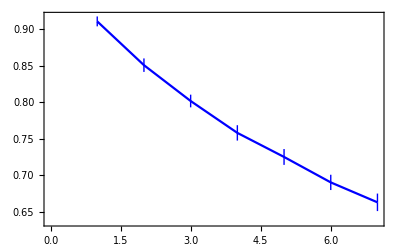

```mathematica
ListLinePlot[%127,Frame->True,PlotStyle->Blue]
```

```mathematica
Dimensions[in[10][[1]]]
```

{602}

```mathematica
Table[Mean[input[x]/input[0]],{x,5,60,5}]
```

{0.949254,0.909763,0.881271,0.854787,0.822991,0.799817,0.784386,0.757002,0.737774,0.728031,0.700261,0.68379}

```mathematica
Interpolation[%42]
```

InterpolatingFunction[…]

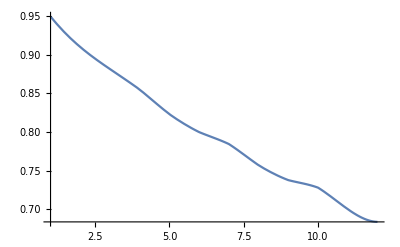

```mathematica
Plot[%107[x],{x,1.,12.}]
```

```mathematica
Sort[%42]
```

{0.68379,0.700261,0.728031,0.737774,0.757002,0.784386,0.799817,0.822991,0.854787,0.881271,0.909763,0.949254}

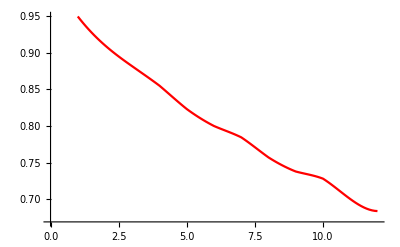

```mathematica
ListLinePlot[Table[{x,%107[x]},{x,Range[1,12,0.1]}],PlotStyle->Red]
```

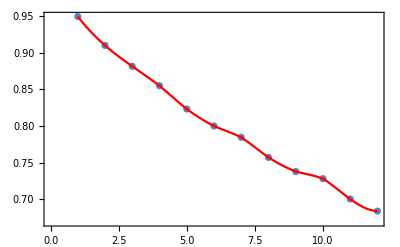

```mathematica
Show[ListPlot[%42,Frame->True],%119]
```

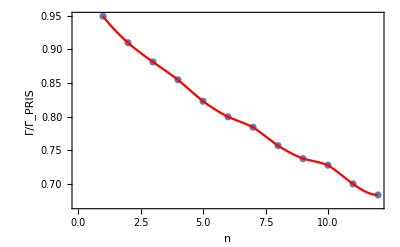

```mathematica
Show[%120,FrameLabel->{{HoldForm[Γ/Subscript[Γ, PRIS]],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```